# Geometria de Distâncias e Geometria Molecular

## Criação da Instância

Códigos

```mathematica
PosicaoPontos[d_, θ_, ω_] := Module[
{B, B1, B2, B3, X, i, di, ct, st, cw, sw, v, numeroAtomos},
numeroAtomos = Length[d];
X = Table[0, {i, numeroAtomos}, {j, 3}]; (* Posição dos Átomos no Espaço *)
{ct,st}={Cos[θ⟦3⟧],Sin[θ⟦3⟧]};
X⟦{1,2,3}⟧={{0,0,0},{-d⟦2⟧,0,0},{-d⟦2⟧+d⟦3⟧ct,d⟦3⟧st ,0}}; (* Três Primeiros Átomos Fixos *)

B1=IdentityMatrix[4];
B2={{-1,0,0,-d⟦2⟧},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d⟦3⟧;
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
B=B1.B2.B3;

For[i = 4, i≤ numeroAtomos, i++,
	{ct, st} = {Cos[θ⟦i⟧], Sin[θ⟦i⟧]}; (* Cos e Sin de theta *)
	{cw, sw} = {Cos[ω⟦i⟧], Sin[ω⟦i⟧]}; (* Cos e Sin de omega *)
	di = d⟦i⟧;  (* Distância do Átomo i até Átomo i-1 *)

	B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}}; (* Matriz de Transformação *)
	v = B.{0,0,0,1}; (* Calcula a posição do Átomo i *)
	X⟦i⟧ = v⟦{1, 2, 3}⟧		
];
Return[X]
];

GerarPontos[numeroAtomos_]:= Module[
	{d, θ, ω, X},

	d = Table[1.526, {i, numeroAtomos}]; (* Tamanho das Ligações Covalentes *)
	d⟦1⟧ = 0;

	θ = Table[1.91, {i, numeroAtomos}]; (* Ângulos Planos *)
	θ ⟦{1, 2}⟧ = {0, 0};

	ω = Table[RandomReal[{0, 2 Pi}], {i, numeroAtomos}]; (* Ângulos de Torção *)
	ω⟦{1,2,3}⟧ = {0,0,0};

	X = PosicaoPontos[d, θ, ω];

	Return[<|"Pontos"->X,"Distancias"->d,"AngulosPlanos"->θ, "AngulosTorcao"->ω|>]
	
];

MostrarPontos[X_,r_,d_]:=Module[{objs={},single,k,Y},
(* Mostrar os Pontos usando as coordenadas em X["Pontos"] *)
single=Length[X⟦1⟧⟦1⟧]==0;
If[single,Y={X},Y=X];
For[k=1,k≤Length[Y],k++,
objs=Union[objs,Table[{Yellow,Sphere[Y⟦k⟧⟦i⟧,r]},{i,3}]];
objs=Union[objs,Table[{Green,Sphere[Y⟦k⟧⟦i⟧,r]},{i,3,Length[Y⟦k⟧]}]];
AppendTo[objs,{Gray,Tube[Y⟦k⟧,d]}];
];
Graphics3D[
objs,
Axes->False,
Boxed->False]
];

MostrarPontos[X_]:=Print[TableForm[X, TableHeadings -> {Table[i, {i, Length[X]}], {"x", "y", "z"}}]]; 
ArestasCompletas[n_] := Module[
{i, j, k = 0, pij},
pij = Table[0, {i, n(n-1)/2}];
For[i=1,i≤n,i++,
For[j=i+1, j≤ n, j++,
k++;
pij⟦k⟧ = i<-> j;
];
];

Return[pij]
];

ArestasMDGP[n_] :=Module[
{E, i, j},
E = List[];
For[i=1,i≤n,i++, 
For[j=i+1, j≤Min[i+3, n], j++, 
AppendTo[E, i<->j]
]
];
Return[E]
];

GerarArestas[x_, r_:-1] := Module[
{numeroAtomos, E, i, j, d},
numeroAtomos = Length[x];
E = List[];
If[r == -1, E = ArestasCompletas[numeroAtomos],
	
	For[i=1,i≤numeroAtomos, i++,
		For[j=i+1, j≤ numeroAtomos, j++,
		d = N[Norm[x⟦i⟧ - x⟦j⟧]];
		If[ d ≤ r,AppendTo[E, i<->j]];
	   ];
	]; 
];

E = E∪ArestasMDGP[numeroAtomos];
Return[E]
];

GerarGrafo[x_, eij_ : {}] := Module[
	{i, j, d, dij, k, numeroAtomos, G, M, E, DijEps},
	If[Length[eij] > 0, E = eij, E = GerarArestas[x]]; (* Inicia a lista de Arestas *)
	(* If[Length[dijEps] > 0, DijEps = dijEps, DijEps = Table[0, {i, Length[E]}]];  Erro em cada aresta *)

	i = Table[E⟦k⟧⟦1⟧, {k, Length[E]}];
	j = Table[E⟦k⟧⟦2⟧, {k, Length[E]}];
	d = Table[N[Norm[x⟦i⟦k⟧⟧ -  x⟦j⟦k⟧⟧]], {k, Length[E]}]; (* Lista de Distâncias *)

	numeroAtomos = Max[i, j];
	M = Table[∞, {i, 1, numeroAtomos}, {j, 1, numeroAtomos}]; (* Matriz de Distâncias *)
	For[k=1, k≤ Length[i], k++,
		M⟦ i⟦k⟧ ⟧⟦ j⟦k⟧ ⟧ = d⟦k⟧;
		M⟦ j⟦k⟧ ⟧⟦ i⟦k⟧ ⟧ = d⟦k⟧;
	];

	G = WeightedAdjacencyGraph[M]; (* Grafo ponderado *) 
	Return[<|"X"->x,"G"->G, "M" ->M|>]
];
```

Exemplos

```mathematica
numeroAtomos = 12;
X = GerarPontos[numeroAtomos]⟦"Pontos"⟧; (*Molécula gerada*)
MostrarPontos[X]; (*Mostra posições no espaço*)
MostrarPontos[X,.1,.04] (* Mostra estrutura gráficamente *)
```

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | -0.469976
5 | -3.64297 | 0.552663 | -1.68279
6 | -4.67677 | 1.14733 | -2.63479
7 | -6.04652 | 1.14588 | -1.96215
8 | -7.10741 | 1.57957 | -2.96967
9 | -8.29807 | 0.628052 | -2.89458
10 | -7.9998 | -0.624176 | -3.71411
11 | -6.59695 | -1.12537 | -3.38319
12 | -5.83306 | -0.0379448 | -2.63309

-Graphics3D-

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,3<->6,4<->5,4<->6,4<->7,4<->12,5<->6,5<->7,5<->8,5<->11,5<->12,6<->7,6<->8,6<->9,6<->10,6<->11,6<->12,7<->8,7<->9,7<->10,7<->11,7<->12,8<->9,8<->10,8<->11,8<->12,9<->10,9<->11,9<->12,10<->11,10<->12,11<->12}

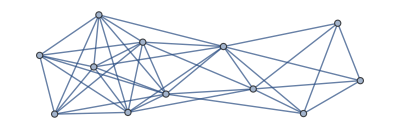

(∞ | 1.526 | 2.49139 | 3.80994 | 4.05073 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1.526 | ∞ | 1.526 | 2.49139 | 2.76021 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 3.74336 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
3.80994 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 2.98132 | ∞ | ∞ | ∞ | ∞ | 3.52854
4.05073 | 2.76021 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 3.83575 | ∞ | ∞ | 3.7991 | 2.45935
∞ | ∞ | 3.74336 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 3.66756 | 3.91736 | 3.06796 | 1.65587
∞ | ∞ | ∞ | 2.98132 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 3.16508 | 2.73512 | 1.37737
∞ | ∞ | ∞ | ∞ | 3.83575 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 2.78357 | 2.08653
∞ | ∞ | ∞ | ∞ | ∞ | 3.66756 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139 | 2.56674
∞ | ∞ | ∞ | ∞ | ∞ | 3.91736 | 3.16508 | 2.49139 | 1.526 | ∞ | 1.526 | 2.49139
∞ | ∞ | ∞ | ∞ | 3.7991 | 3.06796 | 2.73512 | 2.78357 | 2.49139 | 1.526 | ∞ | 1.526
∞ | ∞ | ∞ | 3.52854 | 2.45935 | 1.65587 | 1.37737 | 2.08653 | 2.56674 | 2.49139 | 1.526 | ∞)

```mathematica
r = 4.1;
edges = GerarArestas[X, r] (* Gera arestas da molécula gerada X com distâncias de até r. Para um grafo com todas as arestas, r = -1 *)
P = GerarGrafo[X, edges];
G = P⟦"G"⟧ (*Grafo*)
M=P["M"]//MatrixForm (*Matriz de Distâncias*)
nodes=Table[i,{i,Length[VertexList[G]]}];
```

## Branch & Prune

Códigos

```mathematica
ComprimentoAresta[G_, E_] := Module[
	{M,D, i, a, b, d},
	D = List[];
	M = Normal[WeightedAdjacencyMatrix[G]];
	For[i=1, i≤ Length[E], i++,
		a = E⟦i⟧⟦1⟧;
		b = E⟦i⟧⟦2⟧;
		d = M⟦a⟧⟦b⟧;
		AppendTo[D, d];
	];
	Return[D];
];

PontosIniciais[G_, nodes_] :=Module[
	{numeroAtomos, X, a, b, c, dab, dac, dbc, θ},
	numeroAtomos =  Length[VertexList[G]];
	X = Table[{0, 0, 0}, {i, numeroAtomos}];
	{a, b, c} = nodes⟦1;;3⟧;
	{dab, dac, dbc} = ComprimentoAresta[G, {a<->b, a<->c, b<->c}];
	   θ=ArcCos[(dab^2+dbc^2-dac^2)/(2*dab*dbc)];
	 X⟦{a, b, c}⟧ = { {0,0,0}, {-dab, 0,0}, {-dab + dbc Cos[θ], dbc Sin[θ], 0} };
	Return[X]
];

Intersecao3Esferas[a_, ra_, b_, rb_, c_, rc_] := Module[
{AbsCos, u, v, w, du, dv, dw, n, A,x, p, dp, dpu, error},
AbsCos[u_, v_] := Dot[u, v]/(Norm[u] Norm[v]);
{u, v, w, du, dv, dw} = MinimalBy[{
	{AbsCos[b-a, c-a], {a, b, c, ra, rb, rc}},
	{AbsCos[c-b, a-b], {b, c, a, rb, rc, ra}},
	{AbsCos[a-c, b-c], {c, a, b, rc, ra, rb}}
}, First]⟦1⟧⟦2⟧;

n = Normalize[(v - u) × (w - u)];
A = {v - u, w - u, n};
 x = {(Dot[v,v] - dv^2 - Dot[u,u] + du^2)/2, (Dot[w,w]- dw^2 - Dot[u,u] + du^2)/2, n.u}; 
p = LinearSolve[A, x];
{u, du} = MaximalBy[{
	{Abs[ra - Norm[p - a]]/ra,{a, ra}},
	{Abs[rb - Norm[p - b]]/rb,{b, rb}},
	{Abs[rc - Norm[p - c]]/rc,{c, rc}}
}, First]⟦1⟧⟦2⟧;
dpu = Norm[p - u];
dp = N[√(du^2 - dpu^2)];
x = {p + dp n, p - dp n};
 error = Table[Max[Abs[{(Norm[a - x⟦i⟧] - ra)/ra, (Norm[b - x⟦i⟧] - rb)/rb, (Norm[c - x⟦i⟧] - rc)/rc}]],{i, 2}]; 
Return[{x, error}]
];

CalculaPonto[G_, X_, branch_, nodes_, i_] :=Module[
{k, vizinhos, i1, i2, i3, d1, d2, d3, x, erro},

k = nodes⟦i⟧;
vizinhos = AdjacencyList[G, k]∩ nodes⟦1;;(i-1)⟧;
i1 = vizinhos⟦1⟧;
i2 = vizinhos⟦2⟧;
i3 = vizinhos⟦3⟧;

{d1, d2, d3} =  ComprimentoAresta[G, {i1<->k, i2<->k, i3<->k}];
{x, erro} = Intersecao3Esferas[X⟦i1⟧, d1, X⟦i2⟧, d2, X⟦i3⟧, d3];
Return[x⟦branch + 1⟧]
];


ResiduoRelativo[G_,X_,nodes_,i_]:= Module[
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij,nid},
Xi=X⟦nodes⟦i⟧⟧;
nid=Table[0,{k,i}]; 
For[k=1,k≤i,k++,
nid⟦nodes⟦k⟧⟧=k
];
V= Select[AdjacencyList[G,nodes⟦i⟧],MemberQ[nid,#]&];
errorDij=0.0; 
For[k=1,k≤Length[V],k++,
j=V⟦k⟧;
Xj=X⟦j⟧;
Dij=EuclideanDistance[Xi,Xj];
{Lij} = ComprimentoAresta[G, {i<->j}];
eij = Abs[(Lij - Dij)/Lij]; 
errorDij = Max[errorDij, eij];
];
Return[errorDij]
];

BranchPrune[G_, nodes_]:=Module[
	{numeroAtomos, X, branch, prune, work, S, k, tolerancia = 10^-6, error, i},
	numeroAtomos = Length[VertexList[G]];
	X = PontosIniciais[G, nodes⟦1;;3⟧];

	branch = Table[0, {i, numeroAtomos}];
	branch⟦1;;3⟧ = 1;
	
	work = Table[0, {i, numeroAtomos}];
	work⟦1;;3⟧ = 1;

	S = <|"Pontos" -> {}, "Branches" -> {}|>;
	k = 4;
	
	While[k > 3,
		work⟦k⟧++;
		X⟦nodes⟦k⟧⟧ = CalculaPonto[G, X, branch⟦k⟧, nodes, k];
		error = ResiduoRelativo[G,X, nodes, k];
		prune = error > tolerancia;
				
		If[Not[prune] && k == numeroAtomos,
			AppendTo[S["Pontos"], X];
			AppendTo[S["Branches"], branch]; 
		];
		
		prune = prune || k==Length[branch];
		If[prune && branch⟦k⟧ == 1, 
			While[k > 3 && branch⟦k⟧ == 1, k--]
	      ];
		If[prune && branch⟦k⟧ == 0, 
			branch⟦k⟧ = 1;
			For[i = k+1, i ≤ Length[branch], i++, branch⟦i⟧ = 0];
		];
		If[Not[prune], k++];
	];

	Print["Branch & Prune"];
	Print["Número de Soluções: ",Length[S["Pontos"]]];
	
	Return[{S, work}];
];

MostrarSolucoes[S_]:=Module[{},
	For[i=1,i≤Length[S],i++,
		Print["Solução ", i,":"];
		MostrarPontos[S⟦i⟧];
			Print[MostrarPontos[S⟦i⟧,.1,.04]]
	]
];
```

Exemplos

```mathematica
{S,work}=BranchPrune[G,nodes]; (*Gera as soluções *)

MostrarSolucoes[S["Pontos"]]
```

Branch & Prune

Número de Soluções: 8

Solução 1:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | -0.469976
5 | -3.64297 | 0.552663 | -1.68279
6 | -5.01914 | -0.105792 | -1.64732
7 | -6.09701 | 0.961093 | -1.81654
8 | -7.46011 | 0.288664 | -1.95243
9 | -8.22022 | 0.912984 | -3.11911
10 | -7.75278 | 0.279931 | -4.42656
11 | -6.2279 | 0.225397 | -4.44761
12 | -5.69122 | 0.48121 | -3.04218

-Graphics3D-

Solução 2:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | -0.469976
5 | -3.64297 | 0.552663 | -1.68279
6 | -5.01914 | -0.105792 | -1.64732
7 | -5.10543 | -1.03725 | -0.441662
8 | -6.4123 | -1.823 | -0.499583
9 | -6.13119 | -3.29708 | -0.222542
10 | -5.64381 | -3.97031 | -1.50235
11 | -4.57872 | -3.09822 | -2.16092
12 | -4.60614 | -1.70557 | -1.53765

-Graphics3D-

Solução 3:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | -0.469976
5 | -3.64297 | 0.552663 | -1.68279
6 | -4.67677 | 1.14733 | -2.63479
7 | -4.14911 | 2.46298 | -3.19987
8 | -5.10239 | 2.97136 | -4.27758
9 | -4.30063 | 3.4029 | -5.50218
10 | -3.96422 | 2.17715 | -6.34659
11 | -3.44119 | 1.06522 | -5.44175
12 | -3.75672 | 1.40336 | -3.98752

-Graphics3D-

Solução 4:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | -0.469976
5 | -3.64297 | 0.552663 | -1.68279
6 | -4.67677 | 1.14733 | -2.63479
7 | -6.04652 | 1.14588 | -1.96215
8 | -7.10741 | 1.57957 | -2.96967
9 | -8.29807 | 0.628052 | -2.89458
10 | -7.9998 | -0.624176 | -3.71411
11 | -6.59695 | -1.12537 | -3.38319
12 | -5.83306 | -0.0379448 | -2.63309

-Graphics3D-

Solução 5:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | 0.469976
5 | -3.64297 | 0.552663 | 1.68279
6 | -4.67677 | 1.14733 | 2.63479
7 | -6.04652 | 1.14588 | 1.96215
8 | -7.10741 | 1.57957 | 2.96967
9 | -8.29807 | 0.628052 | 2.89458
10 | -7.9998 | -0.624176 | 3.71411
11 | -6.59695 | -1.12537 | 3.38319
12 | -5.83306 | -0.0379448 | 2.63309

-Graphics3D-

Solução 6:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | 0.469976
5 | -3.64297 | 0.552663 | 1.68279
6 | -4.67677 | 1.14733 | 2.63479
7 | -4.14911 | 2.46298 | 3.19987
8 | -5.10239 | 2.97136 | 4.27758
9 | -4.30063 | 3.4029 | 5.50218
10 | -3.96422 | 2.17715 | 6.34659
11 | -3.44119 | 1.06522 | 5.44175
12 | -3.75672 | 1.40336 | 3.98752

-Graphics3D-

Solução 7:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | 0.469976
5 | -3.64297 | 0.552663 | 1.68279
6 | -5.01914 | -0.105792 | 1.64732
7 | -5.10543 | -1.03725 | 0.441662
8 | -6.4123 | -1.823 | 0.499583
9 | -6.13119 | -3.29708 | 0.222542
10 | -5.64381 | -3.97031 | 1.50235
11 | -4.57872 | -3.09822 | 2.16092
12 | -4.60614 | -1.70557 | 1.53765

-Graphics3D-

Solução 8:

| x | y | z
1 | 0 | 0 | 0
2 | -1.526 | 0 | 0
3 | -2.03376 | 1.43905 | 0
4 | -3.48534 | 1.4653 | 0.469976
5 | -3.64297 | 0.552663 | 1.68279
6 | -5.01914 | -0.105792 | 1.64732
7 | -6.09701 | 0.961093 | 1.81654
8 | -7.46011 | 0.288664 | 1.95243
9 | -8.22022 | 0.912984 | 3.11911
10 | -7.75278 | 0.279931 | 4.42656
11 | -6.2279 | 0.225397 | 4.44761
12 | -5.69122 | 0.48121 | 3.04218

-Graphics3D-